```mathematica
ClearAll[Evaluate[Context[]<>"*"]];

refPdf[n_,t_]:=PDF[StudentTDistribution[n],t];
refCdf[n_,t_]:=CDF[StudentTDistribution[n],t];

ink[z_,n_?EvenQ]:=Block[{k=n/2,sum=0,nextTerm=0,refSum=0},
sum=0;
nextTerm=z√π/2;
For[j=1,j≤k-1,++j,
sum=sum+nextTerm;
nextTerm=(nextTerm)(z)(j+1/2)/(j+1);
];
refSum=Sum[(z^j Gamma[j+1/2])/(j!),{j,1,k-1}];
Print[refSum==sum//FullSimplify];
1-√(1-z)(1+refSum/√π)
];
ink[z_,n_?OddQ]:=Block[{k=(n-1)/2,sum=0,nextTerm=0,refSum=0},
sum=0;
nextTerm=2z/√π;
For[j=1,j≤k,++j,
sum=sum+nextTerm;
nextTerm=(nextTerm)(z)(j)/(j+1/2);
];
refSum=Sum[(z^j(j-1)!)/Gamma[j+1/2],{j,1,k}];
Print[refSum==sum//FullSimplify];
BetaRegularized[z,1/2,1/2]-(refSum)(√((1-z)/(z π)))
];
myCdf[n_,t_]:=If[t>0,
1-1/2 ink[n/(t^2+n),n],1/2 ink[n/(t^2+n),n]
];

(*Tests*)
testN=3;
testT=3/2;

(*Check the implementation of Regularized Incomplete Beta*)
ink[zz,testN]==BetaRegularized[zz,testN/2,1/2]//FullSimplify
(*Check the implementation of Student's t-Distribution*)
myCdf[testN,testT]==refCdf[testN,testT]//N
1-refCdf[testN,testT]//N
```

True

√(-(-1+zz) zz)==√(-1+1/zz) zz

True

True

0.115292

0.391827

0.391827

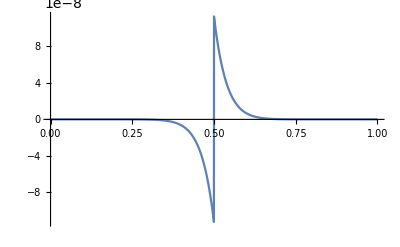

, , -0.666666666666667-0.342857142857143-0.303030303030303-0.287179487179487,

, , -0.278637770897833-0.273291925465839-0.26962962962963-0.266963292547275

, , -0.133333333333333-0.19047619047619-0.20979020979021-0.219607843137255,

, , -0.225563909774436-0.229565217391304-0.232439335887612-0.234604105571848

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];

dOdd[m_]:=-(2(1+m)(1+2m))/((4m+1)(4m+3));
dEven[m_]:=-(2(1+m)(1+2m))/((4m+3)(4m+5));

ink[z_?(#<1/2&),n_]:=Block[{
a0=0,a1=1,a2,
b0=1,b1=1,b2
},
For[m=0,m≤Ceiling[n/2],++m,
a2=a1+z dOdd[m]a0;a0=a1;a1=a2;
a2=a1+z dEven[m]a0;a0=a1;a1=a2;

b2=b1+z dOdd[m]b0;b0=b1;b1=b2;
b2=b1+z dEven[m]b0;b0=b1;b1=b2;
];
(√(z(1-z)))/(π/2)(a2/b2)
];
ink[1/2,n_]:=1/2;
ink[z_?(#>1/2&),n_]:=1-ink[1-z,n];

zz=1/3;
maxRec=6;
ink[zz,maxRec]//N
BetaRegularized[zz,1/2,1/2]//N
Plot[ink[z,maxRec]-BetaRegularized[z,1/2,1/2],{z,0,1},PlotRange->All]

Print[Row[Table[N[dOdd[m],$MachinePrecision],{m,0,3}],", "],","];
Print[Row[Table[N[dOdd[m],$MachinePrecision],{m,4,7}],", "]];

Print[Row[Table[N[dEven[m],$MachinePrecision],{m,0,3}],", "],","];
Print[Row[Table[N[dEven[m],$MachinePrecision],{m,4,7}],", "]];
```